```mathematica
Quit
```

## Axial Vector (Spin-dependent scattering)

Limits for for Spin-Dependent CS Direct Detection experiments
Based on best limit from 1310.8327: Picasso, SIMPLE, COUPP
The numbers have been obtained using plotdigitizer from Figure 9 (right) in 1310.8327
orig publication http://arxiv.org/pdf/1301.6620.pdf

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*90 %CL *)
```

```mathematica
mass=10^{0.6551724,0.7241379,0.7758621,0.8534483,0.8965517,0.94827586,1.0172414,1.0862069,1.1637931,1.25,1.3706896,1.5172414,1.6724138,1.862069,2.0517242,2.2672415,2.474138,2.7327585,3.0086207,3.3017242,3.6034484,3.974138};
xsec=10^{-36.704468,-36.920963,-37.065292,-37.20962,-37.281788,-37.498283,-37.690723,-37.88316,-38.051548,-38.17182,-38.340206,-38.436424,-38.46048,-38.436424,-38.340206,-38.17182,-38.003437,-37.762886,-37.498283,-37.20962,-36.896908,-36.536083};
```

```mathematica
dataSD=Interpolation[Transpose[{mass,xsec}],InterpolationOrder->1]
```

InterpolatingFunction[{{4.52035,9421.89}},<>]

```mathematica
dataSD[5]
```

1.49687×10^-37

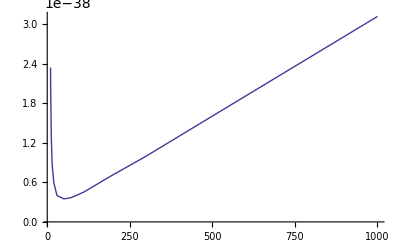

```mathematica
Plot[dataSD[m],{m,10,1000}]
```

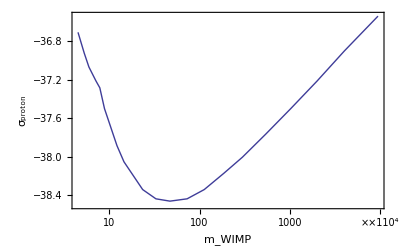

```mathematica
ListLogLinearPlot[Transpose[{mass,Log10[xsec]}],
Joined->True,
Frame->True,
FrameLabel->{Style["m_WIMP",16],Style["σ_proton",16]}
]
```

```mathematica
(*ME2axial[g_,mDM_,ma_]:=g mDM^4/((ma^2-mDM^2)^2); *)
```

```mathematica
(*Axial vector interactions (from 1312.7772 and 1407.8257 Eq.3.10)*)
```

ATTENTION! pΔu and so on are for Wimp-proton CS. That is what we compare to! There are also values for wimp-nucleon scatterings

```mathematica
pΔu=0.787;nΔu=-0.312;
pΔd=-0.319;nΔd=0.787;
pΔs=-0.04;nΔs=-0.04;
a=pΔu+pΔd+pΔs;
μ[mDM_]:=(mDM mp)/(mDM+mp);
mp=1;


σ[mDM_,mMED_,gDM_,gq_]=(3gDM^2*gq^2*a^2 μ[mDM]^2)/(π mMED^4);
gev2tocm2=0.3894 10^-27;
```

```mathematica
σ[5,1388.36,1.0,0.5]*gev2tocm2
```

3.18291×10^-42

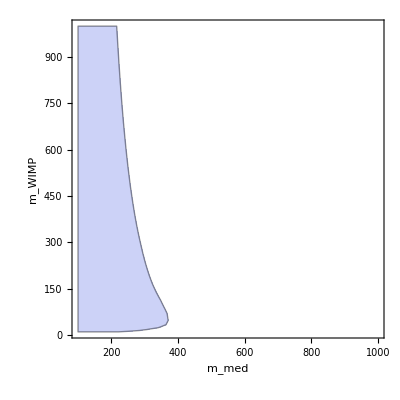

```mathematica
RegionPlot[(*10000*)gev2tocm2*σ[mDM,mMED,1,1]>dataSD[mDM],{mMED,100,1000},{mDM,10,1000},
Frame->True,
FrameLabel->{Style["m_med",16],Style["m_WIMP",16]}
]
```

```mathematica
Export["demo_limit.pdf",%]
```

demo_limit.pdf

## Scalar and Vector (Spin-independent scattering)

Spin-independent interactions from LUX:
Publication http://arxiv.org/pdf/1402.3731v2.pdf
Figure 3
90%CL

```mathematica
massSI={5.76559,5.82183,5.87802,5.94534,6.04606,6.14686,6.2586,6.35908,6.58225,6.78294,7.02807,7.29537,7.54038,7.84102,8.15255,8.48648,8.74248,9.20964,9.45434,9.87704,10.2997,10.6556,11.19,12.6164,15.2342,18.0824,24.4075,32.6639,44.0895,65.3948,83.8453,119.145,167.862,248.978,347.789,507.084,720.573,980.995,1324.14,1865.56,2628.37,3369.94,3965.87};
```

```mathematica
xsSI={10186579,5319695,2920000,1580000,796575,376458,206699,131848,53649.6,28026.9,14642.9,8042.89,4721.9,2593.79,1740.19,988.374,652.061,409.417,319.066,203.68,138.983,101.355,54.9395,33.6866,20.1796,13.9016,9.35617,7.94857,7.94857,9.35617,10.7595,15.259,20.6552,30.6898,40.5865,58.9157,81.63,105.468,149.574,212.124,307.921,397.842,490.627};
xsSI=xsSI*10^(-46);
```

```mathematica
Length[massSI]
Length[xsSI]
```

43

43

```mathematica
dataSI=Interpolation[Transpose[{massSI,xsSI}],InterpolationOrder->1]
```

InterpolatingFunction[{{5.76559,3965.87}},<>]

```mathematica
Table[Log10[dataSI[m]],{m,5.8,10,0.2}]
```

{-39.1421,-39.9375,-40.5291,-40.9299,-41.2892,-41.5671,-41.7911,-41.9831,-42.1788,-42.3665,-42.54,-42.6659,-42.7869,-42.927,-43.0761,-43.2061,-43.2854,-43.3826,-43.4696,-43.5539,-43.6484,-43.7332}

```mathematica
Table[Log10[dataSI[m]],{m,10,1000,10}]
```

{-43.7332,-44.9023,-45.0756,-45.0997,-45.0789,-45.0458,-45.0129,-44.9802,-44.9376,-44.8922,-44.851,-44.8138,-44.7835,-44.7553,-44.7287,-44.7037,-44.6794,-44.6545,-44.6309,-44.6085,-44.5872,-44.567,-44.5476,-44.529,-44.5116,-44.4977,-44.4842,-44.4711,-44.4584,-44.4461,-44.4341,-44.4225,-44.4111,-44.4,-44.3889,-44.3768,-44.3651,-44.3537,-44.3425,-44.3317,-44.3211,-44.3107,-44.3006,-44.2908,-44.2811,-44.2717,-44.2624,-44.2534,-44.2445,-44.2358,-44.2275,-44.2198,-44.2122,-44.2047,-44.1974,-44.1901,-44.183,-44.176,-44.1692,-44.1624,-44.1557,-44.1492,-44.1427,-44.1363,-44.1301,-44.1239,-44.1178,-44.1117,-44.1058,-44.1,-44.0942,-44.0885,-44.0836,-44.0788,-44.0741,-44.0694,-44.0647,-44.0601,-44.0556,-44.0511,-44.0466,-44.0422,-44.0379,-44.0336,-44.0293,-44.0251,-44.0209,-44.0167,-44.0126,-44.0085,-44.0045,-44.0005,-43.9965,-43.9926,-43.9887,-43.9849,-43.981,-43.9773,-43.9721,-43.9669}

```mathematica
(* vector interactions (from 1407.8257) Eq. 3.8 *)
σvqq[mDM_, mMED_,gDM_,gSM_]:=9/Pi*gDM^2*gSM^2*μ[mDM]^2/mMED^4;
μ[mDM_]:=(mDM mp)/(mDM+mp);
mp=0.935;
```

```mathematica
tocm=0.3894 10^-27;
```

```mathematica
σvqq[1, 1567.67,1,0.5]*tocm
```

1.07813×10^-41

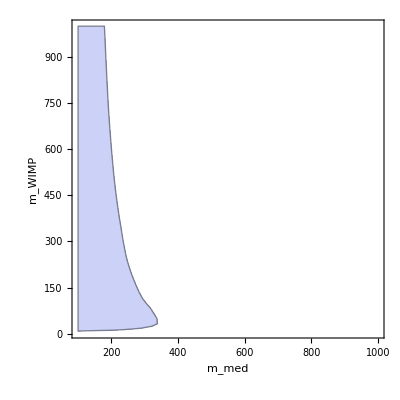

```mathematica
RegionPlot[(*10000*)tocm*σvqq[mDM,mMED,0.01,0.01]>dataSI[mDM],{mMED,100,1000},{mDM,6,1000},
Frame->True,
FrameLabel->{Style["m_med",16],Style["m_WIMP",16]}
]
```

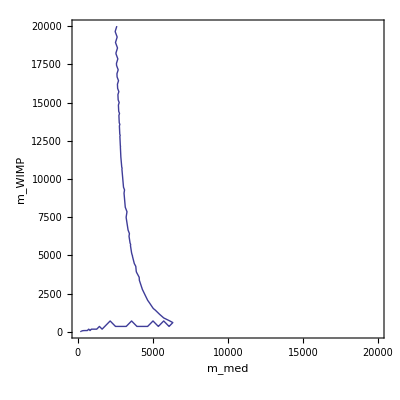

```mathematica
contourCV=ContourPlot[(*10000*)tocm*σvqq[mDM,mMED,Sqrt[0.1],Sqrt[0.1]]==dataSI[mDM],{mMED,10,20000},{mDM,5,20000},
Frame->True,
FrameLabel->{Style["m_med",16],Style["m_WIMP",16]}
]
```

```mathematica
Export["contourCV",contourCV,"TEXT"]
```

contourCV

```mathematica
Export["contourCA",contourA,"TEXT"]
```

contourCA

```mathematica
Export["contourCSg100",contourCS,"TEXT"]
```

contourCSg100

```mathematica
(* Scalar-gluon interactions *)
(*σhgg[mDM_, mMED_,gDM_,gq_]:=3.83 10^-41 μ[mDM]^2(100/(mMED/Sqrt[gDM*gq]))^6;*)
```

```mathematica
(* g^2 = gt * gchi *)
```

```mathematica
σhgX[mDM_,mMED_,g_]:=μ[mDM]^2/Pi*(2/27 1/246 0.9*1/mMED^2*g^2)^2
```

```mathematica
σhgX[100,1000,1]
```

3.78691×10^-21

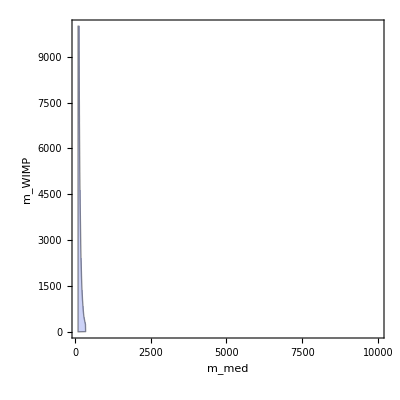

```mathematica
RegionPlot[(*10000*)tocm*σhgX[mDM,mMED,Sqrt[Sqrt[5]]]>dataSI[mDM]*1,{mMED,100,10000},{mDM,6,10000},
Frame->True,
FrameLabel->{Style["m_med",16],Style["m_WIMP",16]}
]
```

```mathematica
RegionPlot[(*10000*)gev2tocm2*σ[mDM,mMED,1,1]>dataSD[mDM],{mMED,100,1000},{mDM,10,1000},Frame->True,FrameLabel->{Style["\!\(\*SubscriptBox[\(m\), \(med\)]\)",16],Style["\!\(\*SubscriptBox[\(m\), \(WIMP\)]\)",16]}]
```

-Graphics-

InterpolatingFunction::dmval: Input value {1.02136} lies outside the range of data in the interpolating function. Extrapolation will be used.

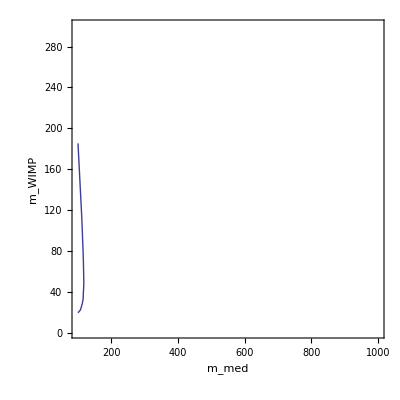

```mathematica
contourA =ContourPlot[(*10000*)gev2tocm2*σ[mDM,mMED,Sqrt[0.1],Sqrt[0.1]]==dataSD[mDM],{mMED,100,1000},{mDM,1,300},Frame->True,FrameLabel->{Style["\!\(\*SubscriptBox[\(m\), \(med\)]\)",16],Style["\!\(\*SubscriptBox[\(m\), \(WIMP\)]\)",16]}]
```

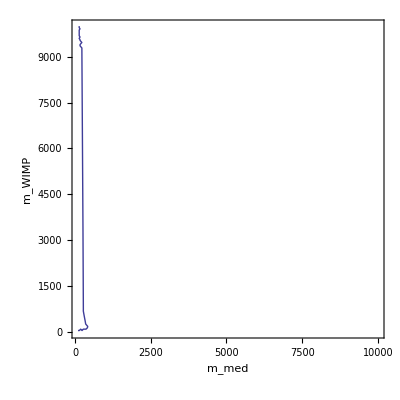

```mathematica
contourCS=ContourPlot[(*10000*)tocm*σhgX[mDM,mMED,Sqrt[Sqrt[5]]]==dataSI[mDM],{mMED,100,10000},{mDM,6,10000},Frame->True,FrameLabel->{Style["\!\(\*SubscriptBox[\(m\), \(med\)]\)",16],Style["\!\(\*SubscriptBox[\(m\), \(WIMP\)]\)",16]}]
```

```mathematica
(* Indirect Detection for Pseudo Scalar *)
```

```mathematica
(* 1108.3546, here 95% CL *)
```

```mathematica
massID={5.00006, 6.42998,8.90673,12.2673,16.514,21.4807,28.5877,37.6131,48.0937,63.2778,82.3095,101.117,127.825,172.075,217.528,289.501,363.889,436.943,542.971,629.993,743.604,908.342,1001.07};
```

```mathematica
xsID={10.4932,12.1095,14.6592,18.6212,23.6565,26.65,31.4996,35.4837,39.9769,46.1302,53.2335,59.9852,72.645,90.0941,114.489,141.996,184.846,229.364,291.492,353.149,427.814,556.984,643.234};
xsID=xsID*10^(-27);
```

```mathematica
dataID=Interpolation[Transpose[{massID,xsID}],InterpolationOrder->1]
```

InterpolatingFunction[{{5.00006,1001.07}},<>]

```mathematica
dataID[5]
```

1.04931×10^-26

```mathematica
Table[Log10[dataID[m]],{m,5,1000,10}]
```

{-25.9791,-25.6603,-25.5368,-25.4643,-25.4128,-25.3688,-25.33,-25.2967,-25.266,-25.2382,-25.2088,-25.1767,-25.1469,-25.1222,-25.1001,-25.079,-25.059,-25.0378,-25.0131,-24.9897,-24.9675,-24.9464,-24.9305,-24.9166,-24.9031,-24.89,-24.8774,-24.865,-24.853,-24.8381,-24.8212,-24.805,-24.7893,-24.7742,-24.7595,-24.7454,-24.7316,-24.7176,-24.704,-24.6908,-24.678,-24.6656,-24.6535,-24.6417,-24.6306,-24.6199,-24.6094,-24.5992,-24.5892,-24.5794,-24.5699,-24.5605,-24.5514,-24.5424,-24.5332,-24.5229,-24.5127,-24.5028,-24.4931,-24.4837,-24.4744,-24.4653,-24.4564,-24.448,-24.4401,-24.4323,-24.4246,-24.4171,-24.4097,-24.4024,-24.3953,-24.3883,-24.3813,-24.3745,-24.3676,-24.3598,-24.352,-24.3444,-24.337,-24.3296,-24.3224,-24.3153,-24.3084,-24.3015,-24.2947,-24.2881,-24.2815,-24.275,-24.2687,-24.2624,-24.2562,-24.2494,-24.2422,-24.2352,-24.2284,-24.2216,-24.2149,-24.2083,-24.2018,-24.1955}

```mathematica
(* this vsgima matches onto the draft *)
```

```mathematica
gamma[g_,mf_,mMED_]:=g^2*mf^2*mMED/8/Pi/(246)^2*(1-mf^2/mMED^2)^0.5
```

```mathematica
gammatot[g_,mDM_,mMED_] :=Re[gamma[g,mDM,mMED]+gamma[g,4.2,mMED]+gamma[g,172,mMED]]
```

```mathematica
gamma[g,2.1,1]
```

(3.27848×10^-22+5.35434×10^-6 ⅈ) g^2

```mathematica
gammatot[1,10,2025]
```

39.403

```mathematica
vsigma[g_,mDM_,mMED_,gammaMED_]:=
3/(2Pi)g^4 4.2^2 mDM^2/246^4*(1/((mMED^2-4 mDM^2)^2+mMED^2*gammaMED^2))Sqrt[1-4.2^2/mDM^2];
gevm2tocm3sm=1.167*10^(-17);
```

```mathematica
gevm2tocm3sm*vsigma[100,100,1000,gammatot[100,100,1000]]
```

4.05519×10^-31

```mathematica
vsigmaG[g_,mDM_,mMED_]:=vsigma[g,mDM,mMED,gammatot[g,mDM,mMED]]
```

```mathematica
gevm2tocm3sm*vsigma[1,10,100,0.4]
```

2.64289×10^-32

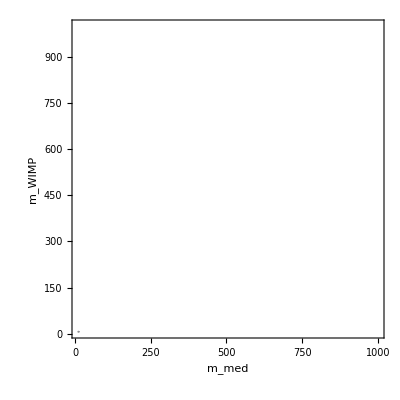

```mathematica
RegionPlot[(*10000*)gevm2tocm3sm*vsigmaG[Sqrt[Sqrt[5]],mDM,mMED]>dataID[mDM],{mMED,10,1000},{mDM,6,1000},
Frame->True,
FrameLabel->{Style["m_med",16],Style["m_WIMP",16]}
]
```

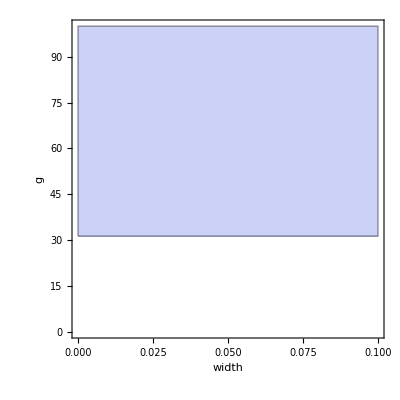

```mathematica
RegionPlot[(*10000*)gevm2tocm3sm*vsigma[g,40,200,width]>dataID[40],{width,10^(-3)/100,1/10},{g,0.01,100},
Frame->True,
FrameLabel->{Style["width",16],Style["g",16]}
]
```

```mathematica
contourPS=ContourPlot[(*10000*)gevm2tocm3sm*vsigmaG[Sqrt[Sqrt[5]]*Sqrt[mDM/246.],mDM,mMED]==dataID[mDM],{mMED,10,100},{mDM,6,100},Frame->True,FrameLabel->{Style["\!\(\*SubscriptBox[\(m\), \(med\)]\)",16],Style["\!\(\*SubscriptBox[\(m\), \(WIMP\)]\)",16]}]
```

-Graphics-

```mathematica
Export["contourPS",contourPS,"TEXT"]
```

contourPS

```mathematica
vgammaG[g,10,mMED]
```

vgammaG[g,10,mMED]

```mathematica
v
```

```mathematica
FullSimplify[gevm2tocm3sm*vsigmaG[Sqrt[10],10,mMED]]
```

2.43573×10^-22/(160000.-800. mMED^2+mMED^4+mMED^2 Re[(0.194512 (1-29584/mMED^2)^0.5+0.000657491 (1-100/mMED^2)^0.5+0.000115981 (1-17.64/mMED^2)^0.5) mMED]^2)

```mathematica
Solve[gevm2tocm3sm*vsigmaG[g,10,mMED]==dataID[10],mMED]
```

```mathematica
≤≥
```